```mathematica
boat[n_]:=ImplicitRegion[Abs[y]^n-1<z<0,{y,z}]
underwater[n_,d_,θ_]:=RegionIntersection[boat[n],HalfSpace[RotationMatrix[θ].{0,1},-d]]
```

```mathematica
Manipulate[Show[RegionPlot[boat[n]],RegionPlot[underwater[n,d,θ]],p1=RegionCentroid@boat[n];p2=RegionCentroid@underwater[n,d,θ];Graphics@Line[{p1,p2}],Graphics[PointSize[Large],Point@p1],Graphics[Point@p2]],{n,1,10,1},{d,0.1,.9,.02},{θ,0,Pi/2,.1}]
```

```mathematica
waterline[n_,θ_]:=(
area=Area@boat[n]; 
desiredArea=area*1/2;
Solve[Area@underwater[n,d,θ]==desiredArea,d]/.{{d->x_}}->x
)
```

```mathematica
N@waterline[2,0]
```

0.370039

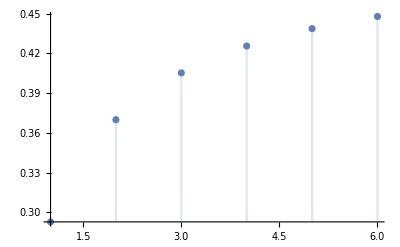

```mathematica
DiscretePlot[waterline[n,0],{n,6}]
```

```mathematica
rightingArm[n_,θ_]:=(
com=RegionCentroid@boat[n];cob=RegionCentroid@underwater[n,waterline[n,θ],θ];
cob[[1]]-com[[1]]
)
```

```mathematica
N@rightingArm[3,1]
```

$Aborted

```mathematica
DiscretePlot[rightingArm[3,θ],{θ,0,Pi/3,Pi/9}]
```

$Aborted

```mathematica
Sort
```